Parte 1 - Probabilidade de outage para o esquema de diversidade Pure Selection da distribuição κ-μ

```mathematica
cdf[g_,k_,m_]:= 1 - MarcumQ[m,√(2k m),√(2 (k+1)m 10^(g/10))];
```

```mathematica
Pout[M_, g_,k_,m_]:=cdf[g,k,m]^M;
```

```mathematica
LogPlot[{Pout[1,x,2,1],Pout[2,x,2,1],Pout[3,x,2,1],Pout[4,x,2,1]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

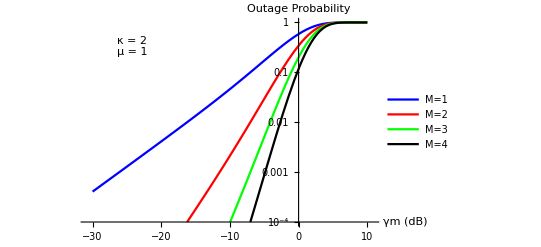

```mathematica
LogPlot[{Pout[1,x,2,2],Pout[2,x,2,2],Pout[3,x,2,2],Pout[4,x,2,2]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

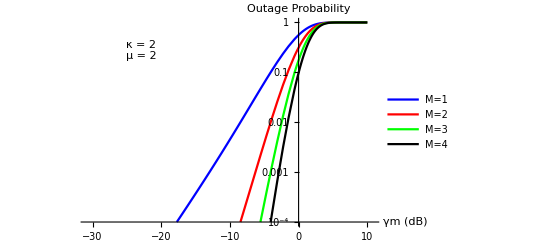

```mathematica
LogPlot[{Pout[1,x,2,3],Pout[2,x,2,3],Pout[3,x,2,3],Pout[4,x,2,3]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

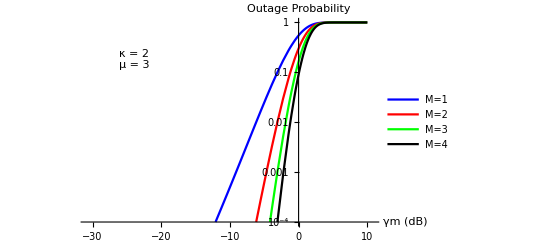

```mathematica
LogPlot[{Pout[1,x,2,4],Pout[2,x,2,4],Pout[3,x,2,4],Pout[4,x,2,4]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

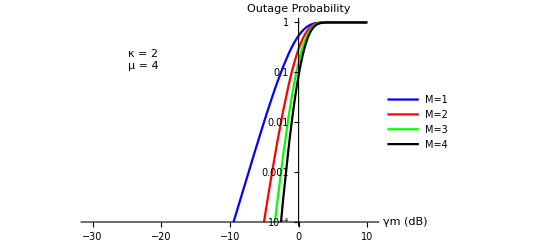

```mathematica
LogPlot[{Pout[1,x,0.0001,2],Pout[2,x,0.0001,2],Pout[3,x,0.0001,2],Pout[4,x,0.0001,2]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

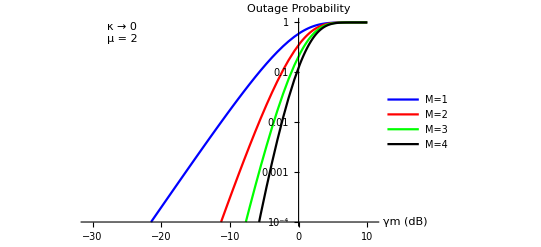

```mathematica
LogPlot[{Pout[1,x,1,2],Pout[2,x,1,2],Pout[3,x,1,2],Pout[4,x,1,2]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

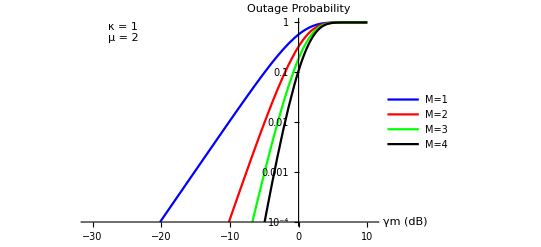

```mathematica
LogPlot[{Pout[1,x,2,2],Pout[2,x,2,2],Pout[3,x,2,2],Pout[4,x,2,2]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

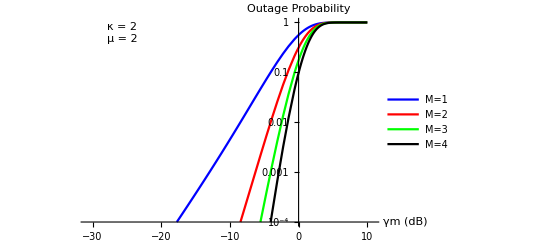

```mathematica
LogPlot[{Pout[1,x,3,2],Pout[2,x,3,2],Pout[3,x,3,2],Pout[4,x,3,2]},{x,-30,10},AxesLabel->{"γm (dB)","Outage Probability "},PlotRange->{10^-4,1},PlotLegends->{"M=1","M=2","M=3","M=4"}, PlotStyle->{Blue,Red,Green,Black}]
```